```mathematica
SetDirectory@NotebookDirectory[]
```

/home/lei/NeuPhysics/codebase/mma/linear-stability

```mathematica
Get["../../neupackage/mma/fourier-mode-growth.wl"]
```

Parameters

```mathematica
dim=11
```

11

Calculation

```mathematica
matRegular[dim,2 ,0.1]//MatrixForm
```

(-10 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1 | -8 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | -6 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.1 | -4 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.1 | -2 | 0.1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 4 | 0.1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 6 | 0.1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 8 | 0.1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 10)

```mathematica
eigenSys[dim,1,0.1][[2,{1,2,3}]]
```

{{0.995074,-0.0990155,0.00493443,-0.000164073,4.09369×10^-6,-8.17384×10^-8,1.36037×10^-9,-1.94098×10^-11,2.42354×10^-13,-2.69015×10^-15,2.68748×10^-17},{0.0990135,0.990086,-0.099502,0.00498329,-0.000166246,4.15817×10^-6,-8.31903×10^-8,1.38682×10^-9,-1.98152×10^-11,2.47722×10^-13,-2.75246×10^-15},{0.004975,0.0995,0.990025,-0.0995008,0.00498335,-0.00016625,4.15834×10^-6,-8.31945×10^-8,1.38691×10^-9,-1.98165×10^-11,2.47706×10^-13}}

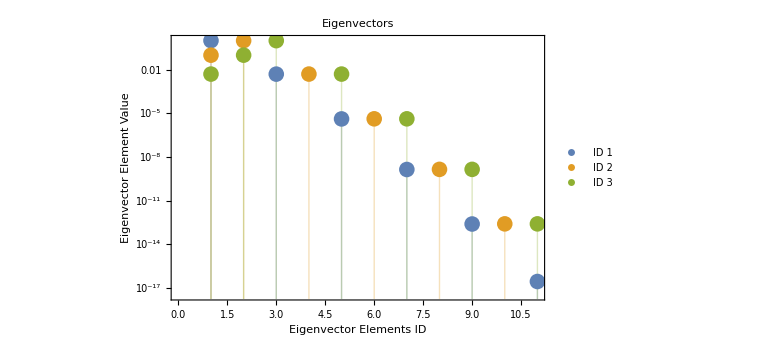

```mathematica
eigenVectorPlot[eigenSys[dim,1,0.1][[2]],{1,2,3},Automatic]
```

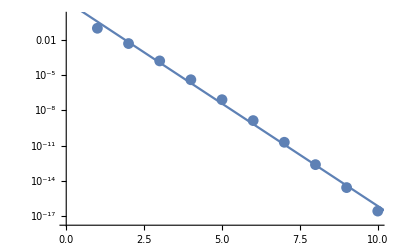

```mathematica
Show[
ListLogPlot[
Abs@eigenSys[dim,1,0.1][[2,1,2;;]]
]
,
Plot[
eigenVecSlopeFit[
eigenSys[dim,1,0.1][[2,1,2;;]] 
].{1,y},
{y,0,dim+1}
]

]
```

```mathematica
evRatioSlope=Table[

{odrat,eigenVecSlopeFit[
eigenSys[101,1,1/odrat][[2,1,2;;]] 
][[2]]},

{odrat,1,100}
];
```

```mathematica
Export["evRatioSlope-dim-101.csv",evRatioSlope]
```

evRatioSlope.csv

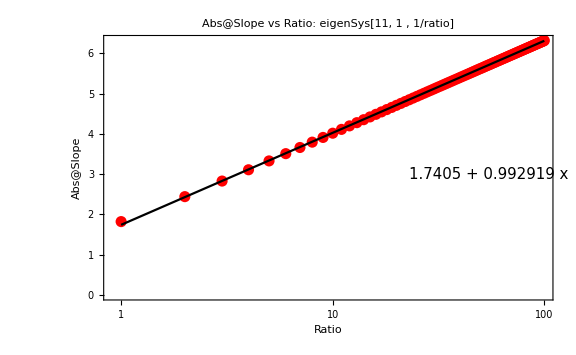

```mathematica
Show[
ListLogLinearPlot[
Abs@evRatioSlope[[1;;]],Frame->True,FrameLabel->{"Ratio","Abs@Slope"},ImageSize->Large,PlotLabel->"Abs@Slope vs Ratio: eigenSys["<>ToString@dim<>", 1 , 1/ratio]",Epilog->Inset[Style[
ToString@Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlope[[1;;]]),
{1,x},x
]
,15],{4,3}],PlotStyle->Red
]
,
LogLinearPlot[
CoefficientList[
Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlope[[1;;]]),
{1,z},z
],z
].{1,Log@y},
{y,1,100},Frame->True,ImageSize->Large,PlotStyle->Black
]

]
```

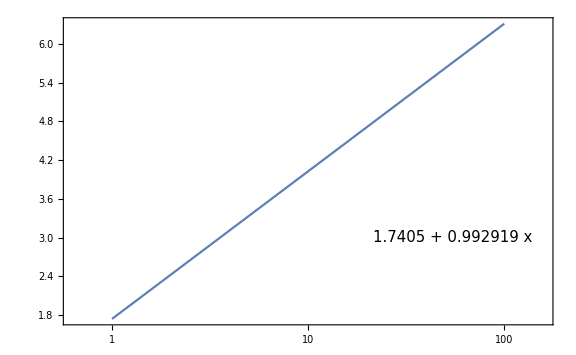

```mathematica
LogLinearPlot[
CoefficientList[
Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlope[[1;;]]),
{1,z},z
],z
].{1,Log@y},
{y,1,100},Frame->True,ImageSize->Large,Epilog->Inset[Style[
ToString@Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlope[[1;;]]),
{1,x},x
]
,15],{4,3}]
]
```

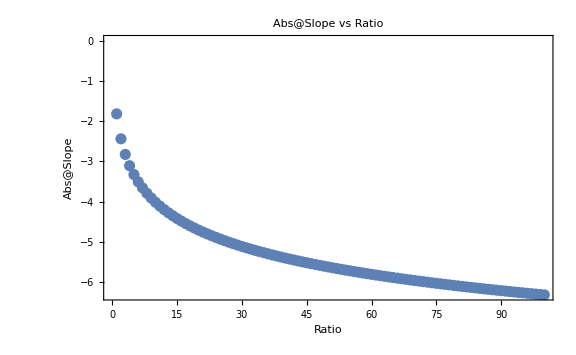

```mathematica
ListPlot[
evRatioSlope,Frame->True,FrameLabel->{"Ratio","Abs@Slope"},ImageSize->Large,PlotLabel->"Abs@Slope vs Ratio"
]
```